```mathematica
FullSimplify[Integrate[2*(1-(r/T)^2)^(alpha/2-1)*Cos[Q*r],{r,0,T}, Assumptions->Q>0&&T>0],Assumptions->Q>0&&T>0]
```

ConditionalExpression[√π T Gamma[alpha/2] Hypergeometric0F1Regularized[(1+alpha)/2,-1/4 Q^2 T^2], Re[alpha]>0]

```mathematica
FullSimplify[(Gamma[alpha/2]*Hypergeometric0F1Regularized[1/2 (1+alpha),-1/4 Q^2 T^2]/Hypergeometric0F1[1/2 (1+alpha),-1/4 Q^2 T^2])]
```

Gamma[alpha/2]/Gamma[(1+alpha)/2]

```mathematica
Asymptotic[Integrate[2*(1-(r/T)^2)^(alpha/2-1)*Cos[Q*r],{r,0,T}, Assumptions->Q>0&&T>0&&Re[alpha]>2]^2,Q->Infinity,Assumptions->Q>0&&T>0&&Re[alpha]>2]
```

2^alpha T^2 (Q T)^-alpha Cos[(alpha π)/4-Q T]^2 Gamma[alpha/2]^2+(2^(-2+alpha) (-2+alpha) alpha T (Q T)^-alpha Cos[(alpha π)/4-Q T] Gamma[alpha/2]^2 Sin[(alpha π)/4-Q T])/Q

```mathematica
TeXForm[2^alpha T^2 (q T)^-alpha Cos[(alpha π)/4-q T]^2 Gamma[alpha/2]^2]
```

2^{\alpha } T^2 \Gamma \left(\frac{\alpha }{2}\right)^2 (q T)^{-\alpha } \cos ^2\left(\frac{\pi  \alpha }{4}-q T\right)

```mathematica
Asymptotic[Integrate[2*Pi*(1-(r/R)^2)^((alpha+1)/2-2)*BesselJ[0,Q*r]*r,{r,0,R}, Assumptions->Q>0&&R>0&&alpha>2],Q->Infinity]
```

(2^(1+alpha/2) √π Q^(-alpha/2) (R^2)^(1-alpha/4) Cos[(alpha π)/4-Q √(R^2)] Gamma[(1+alpha)/2])/(-1+alpha)+(2^(-2+alpha/2) (-2+alpha) alpha √π Q^(-1-alpha/2) (R^2)^(1/2-alpha/4) Gamma[(1+alpha)/2] Sin[(alpha π)/4-Q √(R^2)])/(-1+alpha)

```mathematica
Limit[((R^2 Hypergeometric0F1[(1+alpha)/2,-1/4 Q^2 R^2])/(-1+alpha))^2,Q->Infinity,Assumptions->R>0&&alpha>2]
```

0

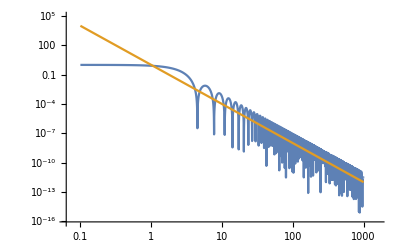

```mathematica
LogLogPlot[{(Hypergeometric0F1[1/2 (1+4),-1/4 Q^2])^2,Q^(-4)},{Q,0.1,1000}]
```

```mathematica
Integrate[2*(1-(r/R)^2)^((alpha+2)/2-2)*Cos[Q*r],{r,0,R}, Assumptions->Q>0&&R>0&&alpha>2]
```

√π R Gamma[alpha/2] Hypergeometric0F1Regularized[(1+alpha)/2,-1/4 Q^2 R^2]

```mathematica
Integrate[(1-(r/R)^2)^((alpha)/2-2)*Sin[Q*r]/(Q*r)*r^2,{r,0,R}, Assumptions->Q>0&&R>0&&alpha>2]
```

1/4 √π R^3 Gamma[-1+alpha/2] Hypergeometric0F1Regularized[(1+alpha)/2,-1/4 Q^2 R^2]